```mathematica
f[x_]:=4Cos[√2 x]-x Sin[1/x]-(x-1/2)Sin[1/(x-1/2)]-(x+1/2)Sin[1/(x+1/2)]
```

{-0.888298,-0.784824,-0.595155,0.0383027,0.595875,0.940728,0.976649}

{0.816829,{x→-0.250006}}

{0.816829,-0.250006}

{0.0923368}

{0.146709}

{0.16377}

{0.19771}

{0.237423}

{0.250585}

{-0.321327}

{-0.331739}

{-0.340522}

{-0.341659}

{-1.,-0.627091,-0.250006,0.0708147,0.259882,0.634988,1.}

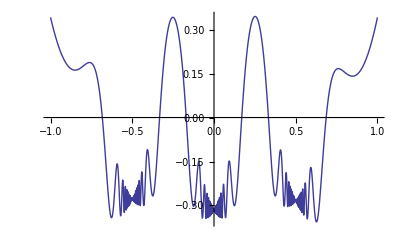

```mathematica
n=6;
point=Sort[RandomReal[{-1,1},n+1]]
interpoint=point;
b=Table[{f[point[[i]]]},{i,n+1}];
a=N[Normal[SparseArray[{{i_,1}:>1,{i_,j_}/;2≤j≤n:>Part[point,i]^(j-1),{i_,n+1}:>(-1)^i},{n+1,n+1}]],6n];
sol=N[Inverse[a].b,6n];
ρs=NMaximize[{Abs[f[x]-sol[[1,1]]-∑_(k=1)^(n-1) (sol[[k+1,1]] x^k)],-1≤x≤1},x]
{ρ,x0}={ρs[[1]],x}/.ρs[[2]]
test=True;
While[test,If[-1≤x0<point[[1]],If[(f[x0]-sol[[1,1]]-∑_(k=1)^(n-1) (sol[[k+1,1]] x0^k))(f[point[[1]]]-sol[[1,1]]-∑_(k=1)^(n-1) (sol[[k+1,1]] point[[1]]^k))≥0,interpoint[[1]]=x0,interpoint=RotateRight[point,1];interpoint[[1]]=x0]];
If[point[[-1]]<x0≤1,If[(f[x0]-sol[[1,1]]-∑_(k=1)^(n-1) (sol[[k+1,1]] x0^k))(f[point[[-1]]]-sol[[1,1]]-∑_(k=1)^(n-1) (sol[[k+1,1]] point[[-1]]^k))≥0,interpoint[[-1]]=x0,interpoint=RotateLeft[point,1];interpoint[[-1]]=x0]];
If[Select[Table[i,{i,1,n}],point[[#]]≤x0&]=!={}&&Select[Table[i,{i,2,n+1}],point[[#]]≥x0&]=!={},j=Last[Select[Table[i,{i,n}],point[[#]]≤x0&]];If[(f[x0]-sol[[1,1]]-∑_(k=1)^(n-1) (sol[[k+1,1]] x0^k))(f[point[[j]]]-sol[[1,1]]-∑_(k=1)^(n-1) (sol[[k+1,1]] point[[j]]^k))≥0,interpoint[[j]]=x0,interpoint[[j+1]]=x0]];
point=interpoint;
b=N[Table[{f[point[[i]]]},{i,n+1}],6n];
a=N[Normal[SparseArray[{{i_,1}:>1,{i_,j_}/;2≤j≤n:>Part[point,i]^(j-1),{i_,n+1}:>(-1)^i},{n+1,n+1}]],6n];
sol=N[Inverse[a].b,6n];
ρs=N[NMaximize[{Abs[f[x]-sol[[1,1]]-∑_(k=1)^(n-1) (sol[[k+1,1]] x^k)],-1≤x≤1},x],6n];
If[Abs[Abs[sol[[-1,1]]]-ρs[[1]]]<10^-n,test=False];
Print[N[sol[[-1]],6n]];
{ρ,x0}={ρs[[1]],x}/.ρs[[2]]
]
point
Plot[f[x]-sol[[1,1]]-∑_(k=1)^(n-1) (sol[[k+1,1]] x^k),{x,-1,1}]
```

{2100.66,{x→-1.}}

{2100.66,-1.}

0.0279517

0.0280597

-0.0303653

-0.0303933

-0.0304138

-0.0304766

-0.0306248

-0.030831

-0.0310583

-0.0312045

-0.0313969

-0.0322491

-0.03226

-0.0322839

-0.0323214

-0.0323722

-0.0324335

-0.0325179

-0.0326586

-0.0332485

-0.0350557

-0.0350846

0.0362425

0.0362468

0.0362535

0.0362651

0.0362825

0.0363067

0.0363396

0.036383

0.0364514

0.0365798

0.036794

0.0378726

0.0499207

0.0697973

0.0748881

0.0787707

0.081174

0.0829542

0.0842572

0.0844658

0.0853194

0.0856813

0.0859688

0.0860777

-0.115014

-0.115476

-0.117532

-0.124918

-0.138678

-0.144532

-0.145018

-0.147473

-0.149624

-0.152127

-0.156034

-0.156195

-0.157608

-0.157641

-0.158687

-0.159633

-0.159642

-0.16029

-0.160291

-0.160291

{-1.,-0.981382,-0.927614,-0.838068,-0.725816,-0.6334,-0.457556,-0.367134,-0.247904,-0.133437,-0.0584389,0.132164,0.246076,0.371407,0.442236,0.62387668239798217597,0.71293046296282853524,0.837199,0.928772,0.982295,1.}

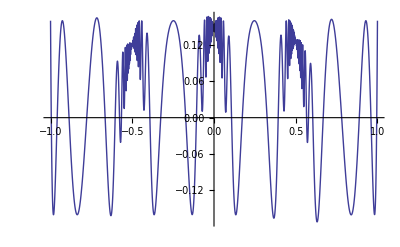

2.94096+0.0168035 x+18.2032 x^2-1.35426 x^3-273.564 x^4+31.3196 x^5+965.774 x^6-299.529 x^7+283.195 x^8+1464.47 x^9-10360. x^10-4052.96 x^11+29099.3 x^12+6612.33 x^13-37683.8 x^14-6300.41 x^15+24052. x^16+3242.17 x^17-6105.86 x^18-696.053 x^19

```mathematica
n=20;
point=Sort[N[RandomInteger[{-10^20,10^20},n+1]/10^20,6n]];
interpoint=point;
b=N[Table[{f[point[[i]]]},{i,n+1}],6n];
a=N[Normal[SparseArray[{{i_,1}:>1,{i_,j_}/;2≤j≤n:>Part[point,i]^(j-1),{i_,n+1}:>(-1)^i},{n+1,n+1}]],6n];
sol=N[Inverse[a].b,6n];
ρs=NMaximize[{Abs[f[x]-sol[[1,1]]-∑_(k=1)^(n-1) (sol[[k+1,1]] x^k)],-1≤x≤1},x]
{ρ,x0}={ρs[[1]],x}/.ρs[[2]]
test=True;
While[test,If[-1≤x0<point[[1]],If[(f[x0]-sol[[1,1]]-∑_(k=1)^(n-1) (sol[[k+1,1]] x0^k))(f[point[[1]]]-sol[[1,1]]-∑_(k=1)^(n-1) (sol[[k+1,1]] point[[1]]^k))≥0,interpoint[[1]]=x0,interpoint=RotateRight[point,1];interpoint[[1]]=x0]];
If[point[[-1]]<x0≤1,If[(f[x0]-sol[[1,1]]-∑_(k=1)^(n-1) (sol[[k+1,1]] x0^k))(f[point[[-1]]]-sol[[1,1]]-∑_(k=1)^(n-1) (sol[[k+1,1]] point[[-1]]^k))≥0,interpoint[[-1]]=x0,interpoint=RotateLeft[point,1];interpoint[[-1]]=x0]];
If[Select[Table[i,{i,1,n}],point[[#]]≤x0&]=!={}&&Select[Table[i,{i,2,n+1}],point[[#]]≥x0&]=!={},j=Last[Select[Table[i,{i,n}],point[[#]]≤x0&]];If[(f[x0]-sol[[1,1]]-∑_(k=1)^(n-1) (sol[[k+1,1]] x0^k))(f[point[[j]]]-sol[[1,1]]-∑_(k=1)^(n-1) (sol[[k+1,1]] point[[j]]^k))≥0,interpoint[[j]]=x0,interpoint[[j+1]]=x0]];
point=interpoint;
b=N[Table[{f[point[[i]]]},{i,n+1}],6n];
a=N[Normal[SparseArray[{{i_,1}:>1,{i_,j_}/;2≤j≤n:>Part[point,i]^(j-1),{i_,n+1}:>(-1)^i},{n+1,n+1}]],6n];
sol=N[Inverse[a].b,6n];
ρs=N[NMaximize[{Abs[f[x]-sol[[1,1]]-∑_(k=1)^(n-1) (sol[[k+1,1]] x^k)],-1≤x≤1},x],6n];
If[Abs[Abs[sol[[-1,1]]]-ρs[[1]]]<10^-10,test=False];
Print[N[sol[[-1,1]],6n]];
{ρ,x0}={ρs[[1]],x}/.ρs[[2]]
]
point
g1=Plot[f[x]-sol[[1,1]]-∑_(k=1)^(n-1) (sol[[k+1,1]] x^k),{x,-1,1}]
Print[sol[[1,1]]+∑_(k=1)^(n-1) (sol[[k+1,1]] x^k)]
```

```mathematica
sol[[1,1]]+∑_(k=1)^(n-1) (sol[[k+1,1]] x^k)
```

2.94096+0.0168035 x+18.2032 x^2-1.35426 x^3-273.564 x^4+31.3196 x^5+965.774 x^6-299.529 x^7+283.195 x^8+1464.47 x^9-10360. x^10-4052.96 x^11+29099.3 x^12+6612.33 x^13-37683.8 x^14-6300.41 x^15+24052. x^16+3242.17 x^17-6105.86 x^18-696.053 x^19

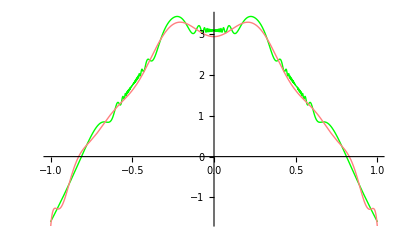

```mathematica
Show[Plot[f[x],{x,-1,1},PlotStyle->{Thick,Green}],Plot[sol[[1,1]]+∑_(k=1)^(n-1) (sol[[k+1,1]] x^k),{x,-1,1},PlotStyle->{Thick,Pink}]]
```

```mathematica
pnt={-1.,-0.9813818962327303,-0.9276144348650002,-0.8380677409190154,-0.7258161170478117,-0.6334001381988549,-0.4575559588576906,-0.367133595166574,-0.24790357759282936,-0.1334365453555474,-0.058438925296807956,0.058438925296807956,0.13216436145150076,0.24607567767603752,0.3714073922134931,0.4422358962410348,0.623876682397982175970000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000001`120.,0.71293046296282853524`120.,0.8371992841876895,0.9287715942408771,0.9822948678503866,1.};
```

```mathematica
{point,RotateRight[point]}ᵀ//MatrixForm
```

(-1. | 1.
-0.981382 | -1.
-0.927614 | -0.981382
-0.838068 | -0.927614
-0.725816 | -0.838068
-0.6334 | -0.725816
-0.457556 | -0.6334
-0.367134 | -0.457556
-0.247904 | -0.367134
-0.133437 | -0.247904
-0.0584389 | -0.133437
0.132164 | -0.0584389
0.246076 | 0.132164
0.371407 | 0.246076
0.442236 | 0.371407
0.62387668239798217597 | 0.442236
0.71293046296282853524 | 0.62387668239798217597
0.837199 | 0.71293046296282853524
0.928772 | 0.837199
0.982295 | 0.928772
1. | 0.982295)

```mathematica
mean=Drop[Total[{point,RotateRight[point]}]/2,1]
```

{-0.990691,-0.954498,-0.882841,-0.781942,-0.679608,-0.545478,-0.412345,-0.307519,-0.19067,-0.0959377,0.0368627,0.18912,0.308742,0.406822,0.533056,0.668403572680405355605,0.775065,0.882985,0.955533,0.991147}

```mathematica
point[[1;;11]]
```

{-1.,-0.981382,-0.927614,-0.838068,-0.725816,-0.6334,-0.457556,-0.367134,-0.247904,-0.133437,-0.0584389}

```mathematica
α=mean
```

{-0.990691,-0.954498,-0.882841,-0.781942,-0.679608,-0.545478,-0.412345,-0.307519,-0.19067,-0.0959377,0.0368627,0.18912,0.308742,0.406822,0.533056,0.668403572680405355605,0.775065,0.882985,0.955533,0.991147}

```mathematica
α[[11]]=(0.058438925296807956+0.13216436145150076)/2
```

0.0953016

```mathematica
α
```

{-0.990691,-0.954498,-0.882841,-0.781942,-0.679608,-0.545478,-0.412345,-0.307519,-0.19067,-0.0959377,0.0953016,0.18912,0.308742,0.406822,0.533056,0.668403572680405355605,0.775065,0.882985,0.955533,0.991147}

```mathematica
S[x_]:=∏_(k=1)^n (α[[k]]-x)
```

```mathematica
NMaximize[{Abs[4000S[x]],-1≤x≤1},x]
```

{0.157618,{x→1.}}

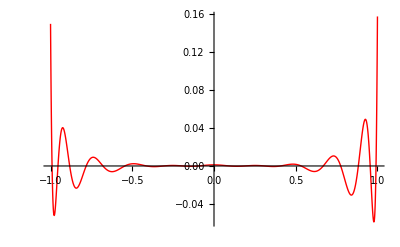

```mathematica
g2=Plot[4000S[x],{x,-1,1},PlotRange->Full,PlotStyle->{Red,Thick}]
```

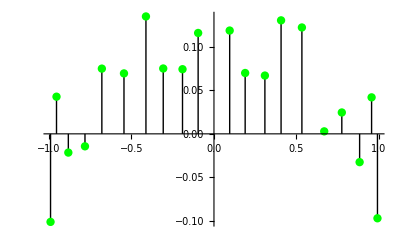

```mathematica
g3=ListPlot[Table[{α[[k]],f[α[[k]]]-sol[[1,1]]-∑_(j=1)^(n-1) (sol[[j+1,1]] α[[k]]^j)},{k,1,n}],PlotStyle->{PointSize[0.015],Green},Filling->Axis,FillingStyle->{Thick,Black}]
```

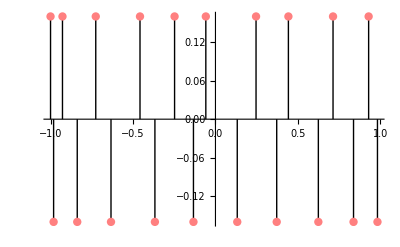

```mathematica
g4=ListPlot[Table[{point[[k]],f[point[[k]]]-sol[[1,1]]-∑_(j=1)^(n-1) (sol[[j+1,1]] point[[k]]^j)},{k,1,n}],PlotStyle->{PointSize[0.015],Pink},Filling->Axis,FillingStyle->{Thick,Black}]
```

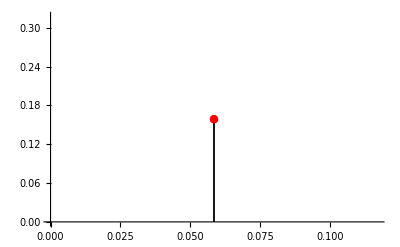

```mathematica
g5=ListPlot[Table[{pnt[[k]],f[pnt[[k]]]-sol[[1,1]]-∑_(j=1)^(n-1) (sol[[j+1,1]] pnt[[k]]^j)},{k,12,12}],PlotStyle->{PointSize[0.015],Red},Filling->Axis,FillingStyle->{Thick,Black}]
```

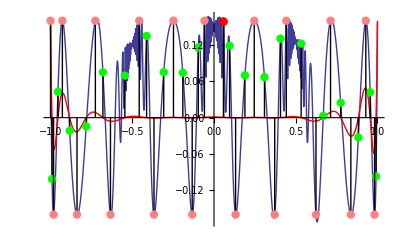

```mathematica
Show[g1,g2,g3,g4,g5]
```

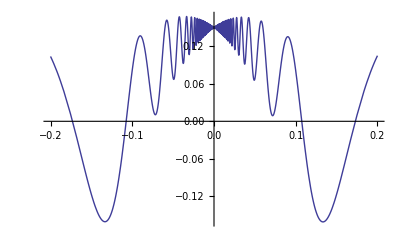

```mathematica
g11=Plot[f[x]-sol[[1,1]]-∑_(k=1)^(n-1) (sol[[k+1,1]] x^k),{x,-0.2,0.2}]
```

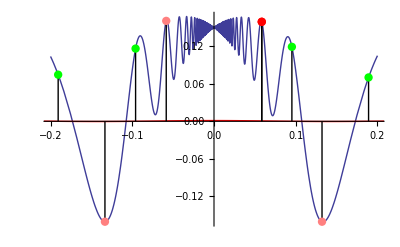

```mathematica
Show[g11,g2,g3,g4,g5]
```